```mathematica
LT[f_,t_,s_]:=∫_(-∞)^∞ f ⅇ^(-s t)ⅆt
```

```mathematica
f[t_]:=(Exp[2t])*UnitStep[t]
```

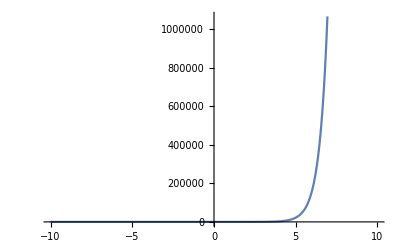

```mathematica
Plot[f[t],{t,-10,10}]
```

```mathematica
F=LT[f[t],t,s]
```

ConditionalExpression[1/(-2+s),Re[s]>2]

```mathematica
LaplaceTransform[Exp[2 t],t,s,GenerateConditions->True]
```

1/(-2+s)

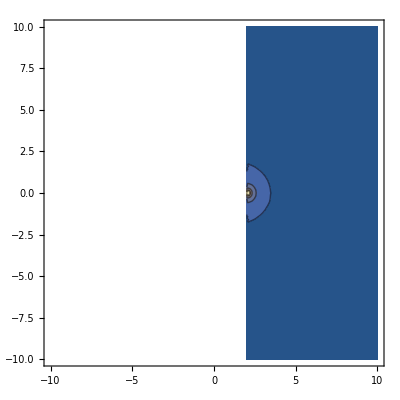
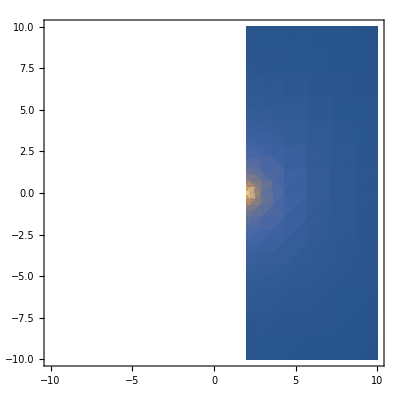
{-Graphics3D-,-Graphics-,-Graphics-}

```mathematica
Block[{s=σ+I ω},Table[plot[Abs[F],{σ,-10,10},{ω,-10,10},PlotRange->Full],{plot,{Plot3D,ContourPlot,DensityPlot}}]]
```